```mathematica
SetDirectory[NotebookDirectory[]]
Get["DataLight.mx"]
Get["../Framework.mx"]
```

/Users/vincent/Code/KayakDynamics/Minimax/2000m tests

## Detailled Automatic Analysis

```mathematica
(*input*)
groups={{1},{2},{3}};
series={{"Stroke Phase",raw},{"Forward Acceleration",filter},{"Right Acceleration",filter},{"Up Acceleration",filter},{"Forward Velocity",filter},{"Right Velocity",filter},{"Up Velocity",filter},{"Forward Distance",filter},{"Right Distance",filter},{"Up Distance",filter},{"Pitch Angular Acceleration",filterangle},{"Yaw Angular Acceleration",filterangle},{"Roll Angular Acceleration",filterangle},{"Pitch Angular Velocity",filterangle},{"Yaw Angular Velocity",filterangle},{"Roll Angular Velocity",filterangle},{"Pitch Angle",filterangle},{"Yaw Angle",filterangle},{"Roll Angle",filterangle}};
tspec={1000,42000};
fspec={90,3};
filter[index_Integer,serie_]:=Take[normalizemean[applybandpassfilter[applybandpassfilter[applybandpassfilter[getData[dataproc,index,serie],fspec],fspec],fspec]],tspec];
filterangle[index_Integer,serie_]:=N[180/π]*filter[index,serie];
raw[index_Integer,serie_]:=Take[getData[dataproc,index,serie],tspec];


(*defs*)
process[groups_List,series_List]:=
Monitor[
Table[series[[serieindex,2]][groups[[groupindex,indexindex]],series[[serieindex,1]]],{groupindex,Length[groups]},{indexindex,Length[groups[[groupindex]]]},{serieindex,Length[series]}],
Grid[{
{ProgressIndicator[groupindex,{1,Length[groups]}]},
{ProgressIndicator[indexindex,{1,Length[groups[[groupindex]]]}]},
{ProgressIndicator[serieindex,{1,Length[series]}]}}
]];

plotranges[res_]:=Module[{serie},
serie=Flatten[Transpose[res,{2,3,1}],{{1},{2,3,4}}];
Return[Table[{Quantile[serie[[i]],0.01],Quantile[serie[[i]],0.99]},{i,Length[serie]}]];
];

scale[x_,{xmin_,xmax_},size_]:=Round[Max[1,Min[size,size*(x-xmin)/(xmax-xmin)]]];

histogram[{x_},{{xmin_,xmax_}},size_]:=Module[{res,imax,ix,inc},
res=Array[0&,{size}];
imax=Length[x];
inc=N[1];
Do[
ix=scale[x[[i]],{xmin,xmax},size];
res[[ix]]+=inc;
,{i,imax}];
Return[res];
];

histogram[{x_,y_},{{xmin_,xmax_},{ymin_,ymax_}},size_]:=Module[{res,imax,ix,iy,inc},
res=Array[0&,{size,size}];
imax=Min[Length[x],Length[y]];
inc=N[1];
Do[
ix=scale[x[[i]],{xmin,xmax},size];
iy=scale[y[[i]],{ymin,ymax},size];
res[[ix,iy]]+=inc;
,{i,imax}];
Return[res];
];

histogram[{x_,y_,z_},{{xmin_,xmax_},{ymin_,ymax_},{zmin_,zmax_}},size_]:=Module[{res,imax,ix,iy,iz,inc},
res=Array[0&,{size,size,size}];;
imax=Min[Length[x],Length[y],Length[z]];
inc=N[1];
Do[
ix=scale[x[[i]],{xmin,xmax},size];
iy=scale[y[[i]],{ymin,ymax},size];
iz=scale[z[[i]],{zmin,zmax},size];
res[[ix,iy,iz]]+=inc;
,{i,imax}];
Return[res];
];

histogram[values_List,ranges_List,size_]:=Module[{res,dim,imax,index,inc},
dim=Min[Length[values],Length[ranges]];
res=Array[0&,Array[size&,dim]];
imax=Min[Map[Length,values]];
inc=N[1];
Do[
index=Table[scale[values[[k]][[i]],ranges[[k]],size],{k,dim}];
res=ReplacePart[res,index->(Extract[res,index]+inc)];
,{i,imax}];
Return[res];
];

makehistograms[res_List,ranges_List,size_]:=Monitor[
Table[
histogram[{res[[groupindex,indexindex,serie1index]],res[[groupindex,indexindex,serie2index]]},{ranges[[serie1index]],ranges[[serie2index]]},size],
{groupindex,Length[res]},{indexindex,Length[res[[groupindex]]]},{serie1index,Length[res[[groupindex,indexindex]]]},{serie2index,Length[res[[groupindex,indexindex]]]}],
Grid[{
{ProgressIndicator[groupindex,{1,Length[res]}]},
{ProgressIndicator[indexindex,{1,Length[res[[groupindex]]]}]},
{ProgressIndicator[serie1index,{1,Length[res[[groupindex,indexindex]]]}]},
{ProgressIndicator[serie2index,{1,Length[res[[groupindex,indexindex]]]}]}}
]];

transcomp=Compile[{{hue,_Real},{sat,_Real},{val,_Real}},
{hue,If[2*(1-((2-sat)*val)/2)+If[2*(1-((2-sat)*val)/2)≤1,(1-((2-sat)*val)/2)*2,2-(1-((2-sat)*val)/2)*2]*If[(2-sat)*val==2||(2-sat)*val==0,0,sat*(val/If[(2-sat)*val≤1,(2-sat)*val,2-(2-sat)*val])]≠0,(2*If[(2-sat)*val==2||(2-sat)*val==0,0,sat*(val/If[(2-sat)*val≤1,(2-sat)*val,2-(2-sat)*val])]*If[(1-((2-sat)*val)/2)*2≤1,(1-((2-sat)*val)/2)*2,2-(1-((2-sat)*val)/2)*2])/((1-((2-sat)*val)/2)*2+If[(2-sat)*val==2||(2-sat)*val==0,0,sat*(val/If[(2-sat)*val≤1,(2-sat)*val,2-(2-sat)*val])]*If[(1-((2-sat)*val)/2)*2≤1,(1-((2-sat)*val)/2)*2,2-(1-((2-sat)*val)/2)*2]),0],(2*(1-((2-sat)*val)/2)+If[2*(1-((2-sat)*val)/2)≤1,(1-((2-sat)*val)/2)*2,2-(1-((2-sat)*val)/2)*2]*If[(2-sat)*val==2||(2-sat)*val==0,0,sat*(val/If[(2-sat)*val≤1,(2-sat)*val,2-(2-sat)*val])])/2}
];
colorinvert=transcomp[#[[1]],#[[2]],#[[3]]]&;

makeGraphs[groups_,seriex_,rangex_,seriey_,rangey_,matrices_List,size_]:=Join[

{Show[Graphics[Raster[ImageData[


ColorConvert[ImageApply[colorinvert,ColorConvert[ColorConvert[Image[Transpose[Table[matrices[[i]]/Max[1,Quantile[Flatten[matrices[[i]]],0.99]],{i,1,Length[matrices]}],{3,1,2}]],"RGB"],"HSB"]],"RGB"]

],{{rangey[[1]],rangex[[1]]},{rangey[[2]],rangex[[2]]}}],AspectRatio->1,Frame->True,Axes->True,FrameLabel->{{None,seriex},{None,seriey}},ImageSize->size]]},

Table[Show[Graphics[Raster[ImageData[ColorConvert[ColorNegate[Image[matrices[[i]]/Max[1,Quantile[Flatten[matrices[[i]]],0.99]]]],"RGB"]],{{rangey[[1]],rangex[[1]]},{rangey[[2]],rangex[[2]]}}],
AspectRatio->1,
Frame->True,
Axes->True,
FrameLabel->{{None,seriex},{None,seriey}},
FrameStyle->Hue[(i-1)/Length[matrices]],
ImageSize->size
]],
{i,1,Length[matrices]}]

];

finalize[groups_List,series_List,ranges_List,matrices_List,size_]:=Module[{res},
res=Transpose[matrices,{3,4,1,2}];(*Transposition to transform group/session/serie1/serie2 to serie1/serie2/group/session*)
res=Map[Total,res,{3}];(*Totals of all sessions within each group, transform serie1/serie2/group/session to serie1/serie2/group*)
res=Flatten[Table[makeGraphs[groups,series[[i,1]],ranges[[i]],series[[j,1]],ranges[[j]],res[[i,j]],300],{i,1,Length[series]},{j,1,Length[series]}],1];
Return[res];
];

(*processing*)
exportGraphs[groups_,series_,filename_]:=Module[{res,ranges,histograms,finale},
res=process[groups,series];
ranges=plotranges[res];
histograms=makehistograms[res,ranges,100];
finale=finalize[groups,series,ranges,histograms,300];
Export[filename,TableForm[finale]];
Return[finale];
];
```

```mathematica
DumpSave["resultat.mx",resultat];
```

```mathematica
Timing[resultat=exportGraphs[groups,series,"Graphsslaala.pdf"];]
EmitSound[Play[Sin[1000t^2],{t,0,1}]]
```

{571.11419,Null}

```mathematica
Export["Resultatslala.html",TableForm[resultat],"GraphicsOutput"->"PNG","MathOutput"->"PNG"];
EmitSound[Play[Sin[1000t^2],{t,0,1}]]
```

## Time Series

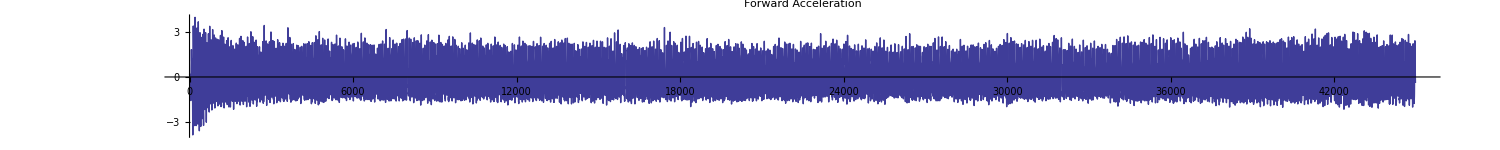
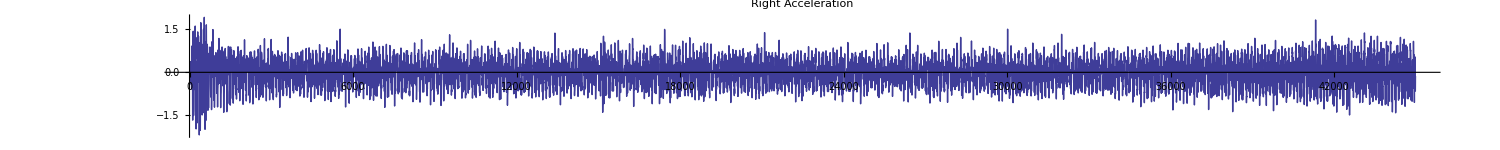
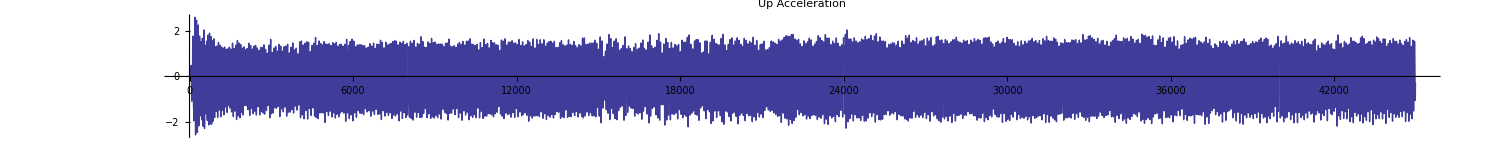
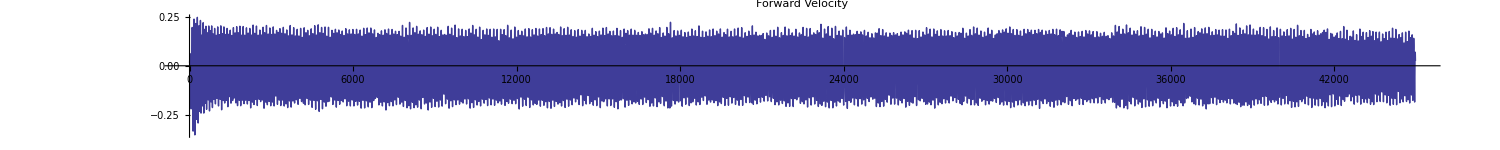
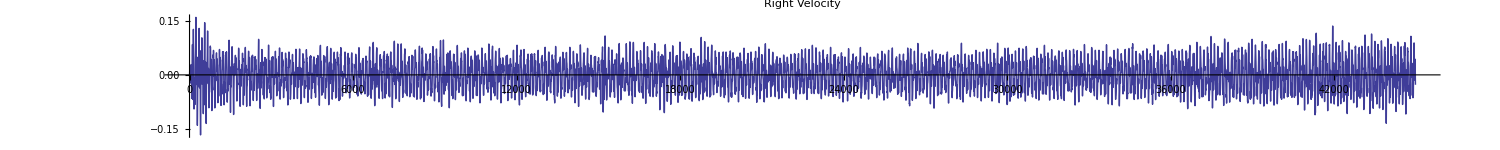
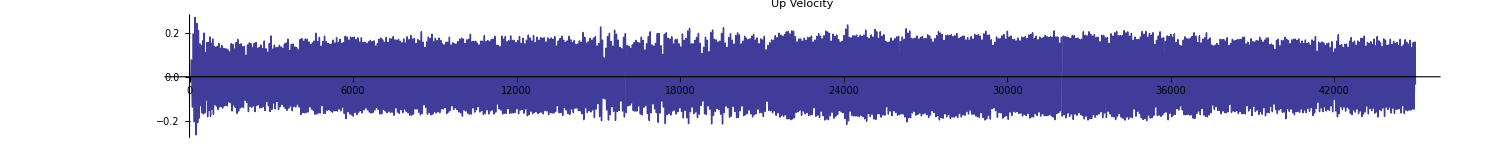
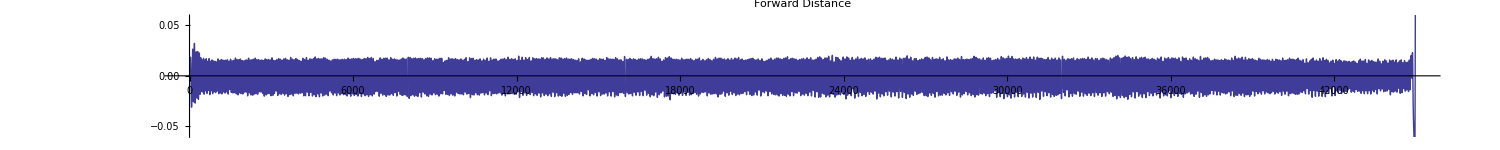
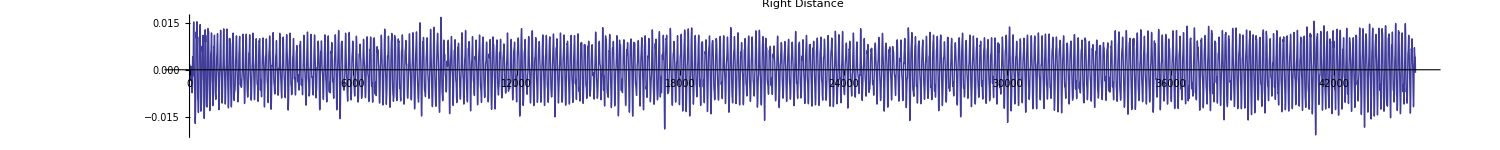

```mathematica
col={"Forward Acceleration","Right Acceleration","Up Acceleration","Forward Velocity","Right Velocity","Up Velocity","Forward Distance","Right Distance","Up Distance","Pitch Angular Acceleration","Yaw Angular Acceleration","Roll Angular Acceleration","Pitch Angular Velocity","Yaw Angular Velocity","Roll Angular Velocity","Pitch Angle","Yaw Angle","Roll Angle","Stroke Phase"};
k=3;
Grid[Transpose[{Table[
ListPlot[{
(*normalizemean[getData[dataproc,k,col[[i]]]],*)
applybandpassfilter[applybandpassfilter[applybandpassfilter[getData[dataproc,k,col[[i]]],{90,3}],{90,3}],{90,3}]
},PlotRange->Automatic,Joined->True,ImageSize->1500,PlotLabel->col[[i]],AspectRatio->0.1]
,{i,Length[col]}]}]]
```

## Divers

```mathematica
dataproc[[1]]
```

{VINCENT LECRUBIER test 2000m toulouse             le 200m avant c'est arnaud 2011/10/21 09:45:42[1956,48561]→1,Etienne HUBERT Test janvier 2012 2000m début propre mais mou fin bien. 2012/01/25 09:01:06[1624,51719]→2,ARNAUD HYBOIS test 200m et 2000m 2012/03/28 10:03:45[1876,46852]→3}

```mathematica
Export["/Volumes/MacBookHD/Users/Vincent/Documents/Minimax/2000m tests/resultats.html",TableForm[resultat],"GraphicsOutput"->"PNG","MathOutput"->"PNG"];
```

```mathematica
Do[Export["/Volumes/MacBookHD/Users/Vincent/Documents/Minimax/2000m tests/resultathtml/"<>series[[i,1]]<>".html",TableForm[Take[resultat,{(i-1)*Length[series]+1,i*Length[series]}]],"GraphicsOutput"->"PNG","MathOutput"->"PNG"];PrintTemporary[i],{i,1,Length[series]}];
```

```mathematica
timeRange[filename_String]:=Import[filename,{"QuickTime","FrameCount"}]/Import[filename,{"QuickTime","FrameRate"}];
timeStep[filename_String]:=1/Import[filename,{"QuickTime","FrameRate"}];

importfile[filename_String]:=Evaluate[ToExpression["data[\""<>ToString[filename]<>"\"]=Import[\""<>ToString[filename]<>"\",{\"QuickTime\",\"ImageList\"}];"]];


filename = "/Volumes/MacBookHD/Users/Vincent/Movies/GOPR0907.MP4";
filename = "/Volumes/MacBookHD/Users/Vincent/Movies/fox-on-the-beach.mp4";
importfile[filename];

timeRange[filename] 
timeStep[filename]
data[filename][[10]]
```

13.5333

0.0334156

```mathematica
ListAnimate[Table[Plot[Sin[n x],{x,0,10}],{n,0,5,0.1}]]
```

```mathematica
Export["/Volumes/MacBookHD/Users/Vincent/Movies/blabla.mov",Table[Plot[Sin[n x],{x,0,10},PlotRange->{All,{-1,1}}],{n,0,5,0.1}]]
```

/Volumes/MacBookHD/Users/Vincent/Movies/blabla.mov

```mathematica
getData[dataproc,3,"Stroke Phase"]
```

{0.950113,0.951247,0.952381,0.953515,0.954649,0.955782,0.956916,0.95805,0.959184,0.960317,0.961451,0.962585,0.963719,0.964853,0.965986,0.96712,0.968254,0.969388,0.970522,0.971655,0.972789,0.973923,0.975057,0.97619,0.977324,0.978458,0.979592,0.980726,0.981859,0.982993,0.984127,0.985261,0.986395,0.987528,0.988662,0.989796,0.99093,0.992063,0.993197,0.994331,0.995465,0.996599,«44893»,0.0892857,0.107143,0.125,0.142857,0.160714,0.178571,0.196429,0.214286,0.232143,0.25,0.267857,0.285714,0.303571,0.321429,0.339286,0.357143,0.375,0.392857,0.410714,0.428571,0.446429,0.464286,0.482143,0.5,0.517857,0.535714,0.553571,0.571429,0.589286,0.607143,0.625,0.642857,0.660714,0.678571,0.696429,0.714286,0.732143,0.75,0.767857,0.785714,0.803571,0.821429}